### 核関数の平滑化距離の変化の影響を確認する

```mathematica
ClearAll["Global`*"];
```

#### 関数の定義 （設定）

```mathematica
a=2187/(40*Pi);
oneThird=1/3;
twoThirds=2/3;
small=10^-10;
wBspline5[q_,h_]:=Module[{qh=q/h},Which[qh≥1,0,qh<oneThird,a/h^3*((1-qh)^5-6*(twoThirds-qh)^5+15*(oneThird-qh)^5),qh<twoThirds,a/h^3*((1-qh)^5-6*(twoThirds-qh)^5),True,a/h^3*(1-qh)^5]]

gradWBspline5[xi_,xj_,h_]:=Module[{r=Norm[xi-xj],c,q,gradQ,dinom=h^4},
If[r*h^4<small,Return[{0.,0.,0.}]];
c=a/dinom;
q=r/h;
gradQ=(xi-xj)/(r*h);
Which[q>1||r*h^4==10^-10,{0.,0.,0.},q<oneThird,gradQ*(5*(1-q)^4-30*(twoThirds-q)^4+75*(oneThird-q)^4)*-c,q<twoThirds,gradQ*(5*(1-q)^4-30*(twoThirds-q)^4)*-c,True,gradQ*(5*(1-q)^4)*-c]]

wBspline3[r_,h_]:=Module[{q=r/h},Which[q>1,0,q<1/2,8*(1-6*q^2+6*q^3)/(Pi*h^3),True,8*2*(1-q)^3/(Pi*h^3)]]

ddrWBspline3[r_,h_]:=Module[{q=r/h,dqdr=1/h},Which[q>1,0,q<1/2,8*(-12*q+18*q^2)*dqdr/(Pi*h^3),True,8*2*3*(1-q)^2*(-dqdr)/(Pi*h^3)]]

gradWBspline3[xi_,xj_,h_]:=Module[{r=Norm[xi-xj],q,dqdr,dinom},
dinom=Pi*h^4*r;
If[dinom<small,Return[{0.,0.,0.}]];
q=r/h;
dqdr=(xi-xj)/(r*h);
Which[q>1||dinom<10^-10,{0.,0.,0.},q<1/2,(xi-xj)*(-96+144*q)*q/dinom,True,-48*(xi-xj)*(1-q)^2/dinom]]
```

```mathematica
(*Set values*)
radius=2.;

(*center*)
A={0.,0.,0.};

vec=Subdivide[-radius,radius,20];

(*Generate Dot_grad_w_Bspline3_Dot,Dot_grad_w_Bspline5_Dot,w_Bspline3,w_Bspline5 values for different x,y,z and plot*)
z=0;
dataBspline3=Flatten[Table[{x,y,wBspline3[Norm[{x,y,z}-A],radius]},{x,vec},{y,vec}],1];
ListPlot3D[dataBspline3,AxesLabel->{"x","y","w_Bspline3"},PlotRange->All]

dataBspline5=Flatten[Table[{x,y,wBspline5[Norm[{x,y,z}-A],radius]},{x,vec},{y,vec}],1];
ListPlot3D[dataBspline5,AxesLabel->{"x","y","w_Bspline5"},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

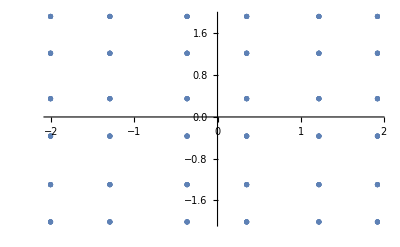

N = 5, sum3 = 1.05361, sum5 = 1.17733

sumGrad3 = {-0.0369066,-0.0369066,-0.0369066}, sumGrad5 = {-0.0149372,-0.0149372,-0.0149372}

Corrected sumGrad3 = {-0.0325529,-0.0325529,-0.0325529}, sumGrad5 = {-0.0131751,-0.0131751,-0.0131751}

B = (0.880729 | 0.000652645 | 0.000652645
0.000652645 | 0.880729 | 0.000652645
0.000652645 | 0.000652645 | 0.880729)

-Graphics3D-

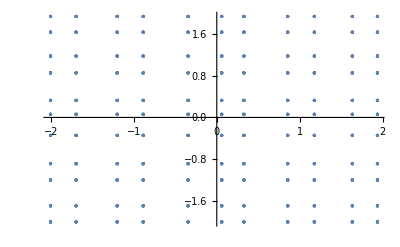

N = 10, sum3 = 0.983443, sum5 = 1.03865

sumGrad3 = {-0.0629689,-0.0629689,-0.0629689}, sumGrad5 = {-0.0546763,-0.0546763,-0.0546763}

Corrected sumGrad3 = {-0.0586956,-0.0586956,-0.0586956}, sumGrad5 = {-0.0509658,-0.0509658,-0.0509658}

B = (0.929503 | 0.00131676 | 0.00131676
0.00131676 | 0.929503 | 0.00131676
0.00131676 | 0.00131676 | 0.929503)

-Graphics3D-

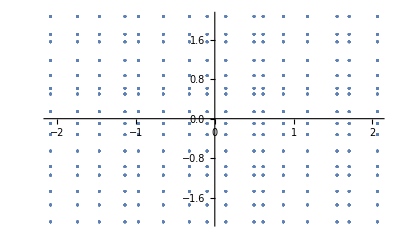

N = 15, sum3 = 1.05813, sum5 = 1.06621

sumGrad3 = {-0.0728095,-0.0728095,-0.0728095}, sumGrad5 = {-0.0625704,-0.0625704,-0.0625704}

Corrected sumGrad3 = {-0.0753988,-0.0753988,-0.0753988}, sumGrad5 = {-0.0647956,-0.0647956,-0.0647956}

B = (1.03227 | 0.00164427 | 0.00164427
0.00164427 | 1.03227 | 0.00164427
0.00164427 | 0.00164427 | 1.03227)

-Graphics3D-

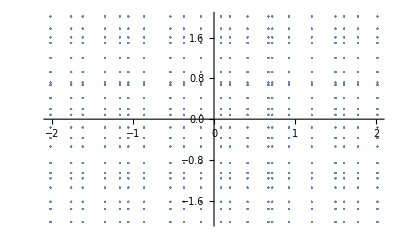

N = 20, sum3 = 1.03033, sum5 = 1.04218

sumGrad3 = {-0.0747165,-0.0747165,-0.0747165}, sumGrad5 = {-0.0716501,-0.0716501,-0.0716501}

Corrected sumGrad3 = {-0.0756876,-0.0756876,-0.0756876}, sumGrad5 = {-0.0725813,-0.0725813,-0.0725813}

B = (1.01007 | 0.00146466 | 0.00146466
0.00146466 | 1.01007 | 0.00146466
0.00146466 | 0.00146466 | 1.01007)

-Graphics3D-

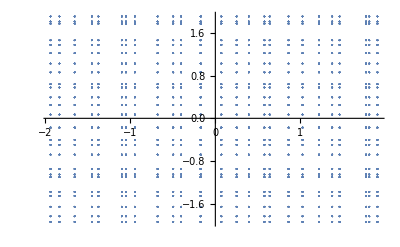

N = 25, sum3 = 1.0649, sum5 = 1.08036

sumGrad3 = {0.011158,0.011158,0.011158}, sumGrad5 = {0.00519717,0.00519717,0.00519717}

Corrected sumGrad3 = {0.0115863,0.0115863,0.0115863}, sumGrad5 = {0.00539663,0.00539663,0.00539663}

B = (1.03842 | -0.0000217858 | -0.0000217858
-0.0000217858 | 1.03842 | -0.0000217858
-0.0000217858 | -0.0000217858 | 1.03842)

```mathematica
(*Calculate sum of w_Bspline3 and w_Bspline5 for different N values and print*)
Do[
sumB=ConstantArray[0,{3,3}];
sum3=0;
sum5=0;
sumGrad3=0;
sumGrad5=0;
totalVolume=(2*radius)^3;
eachVolume=(2*radius/n)^3;
eps=0.1;
V=(#+RandomReal[{-eps,eps}])&/@Subdivide[-radius,radius,n];
points3D={};
points2D={};
Do[
X={x,y,z};
sum3+=wBspline3[Norm[X-A],radius]*eachVolume;
sum5+=wBspline5[Norm[X-A],radius]*eachVolume;

sumGrad3+=gradWBspline3[X,A,radius]*eachVolume;
sumGrad5+=gradWBspline5[X,A,radius]*eachVolume;

sumB+=-TensorProduct[A-X,gradWBspline3[A,X,radius]]*eachVolume;

points3D=Append[points3D,{x,y,z}];
points2D=Append[points2D,{x,y}];
,{x,V},{y,V},{z,V}];

Print[Show[ListPointPlot3D[points3D]]];
Print[Show[ListPlot[points2D]]];

Print["N = ",n,", sum3 = ",sum3,", sum5 = ",sum5];
Print["sumGrad3 = ",sumGrad3,", sumGrad5 = ",sumGrad5];
Print["sumGrad3 = ",sumGrad3.sumB,", sumGrad5 = ",sumGrad5.sumB, "CORRECTED"];
Print[ "B = ",MatrixForm@sumB];

,{n,{5,10,15,20,25}}]
```